#### Problem 9.3.19

Part B

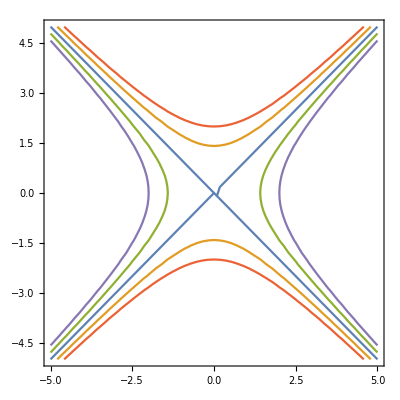

```mathematica
ContourPlot[{0.5*((y^2)-(x^2))==0,0.5*((y^2)-(x^2))==1,0.5*((y^2)-(x^2))==-1,0.5*((y^2)-(x^2))==2,0.5*((y^2)-(x^2))==-2},{x,-5,5},{y,-5,5}]
```

Part C

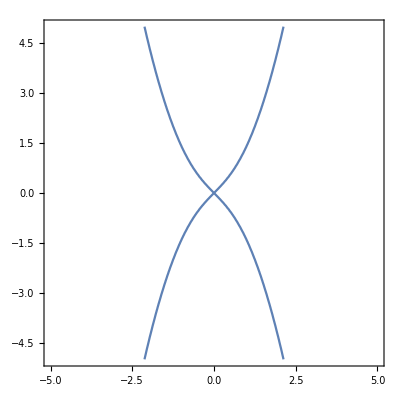

```mathematica
ContourPlot[0.5*((y^2)-(x^2)-(x^4))==0,{x,-5,5},{y,-5,5}]
```

#### Problem 9.3.20

Part B

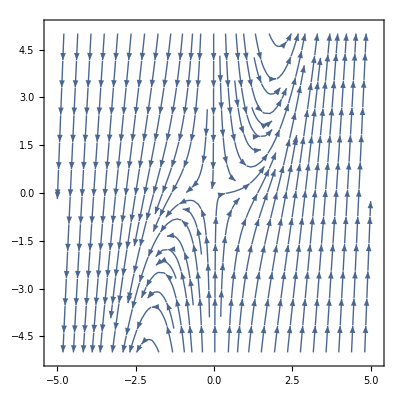

```mathematica
StreamPlot[{x,-2y+(x^3)},{x,-5,5},{y,-5,5}]
```

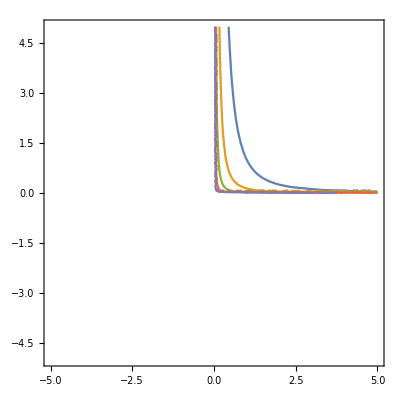

```mathematica
ContourPlot[{-Log[x]-0.5*Log[y]==0,-Log[x]-0.5*Log[y]==1,-Log[x]-0.5*Log[y]==2,-Log[x]-0.5*Log[y]==3,-Log[x]-0.5*Log[y]==4},{x,-5,5},{y,-5,5}]
```

```mathematica
StreamPlot[{x,-2*y+(x^3)},{x,-10,10},{y,-10,10}]
```

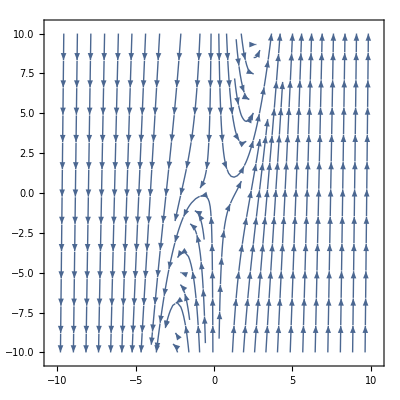

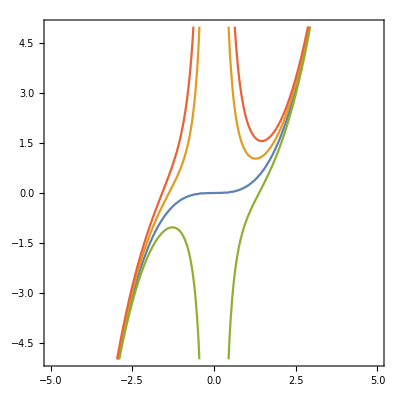

```mathematica
ContourPlot[{y*(x^2)-(1/5)*(x^5)==0,y*(x^2)-(1/5)*(x^5)==1,y*(x^2)-(1/5)*(x^5)==-1,y*(x^2)-(1/5)*(x^5)==2},{x,-5,5},{y,-5,5}]
```

#### Problem 9.3.21

Part D

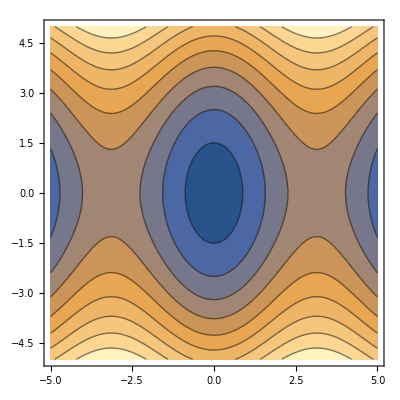

```mathematica
ContourPlot[{0.5*(y^2)-Pi*Cos[x]},{x,-5,5},{y,-5,5}]
```

#### Problem 9.4.1

Part A

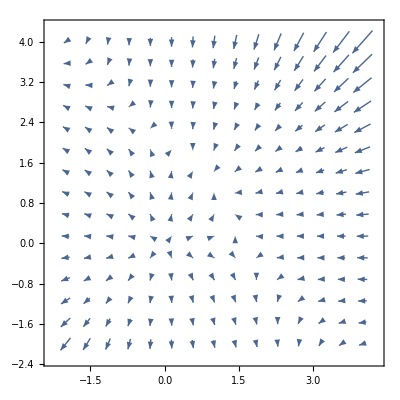

```mathematica
VectorPlot[{x*(1.5-x-0.5*y),y*(2-y-0.75*x)},{x,-2,4},{y,-2,4}]
```

Part B

```mathematica
Solve[{0==x*(1.5-x-0.5*y),0==y*(2-y-0.75*x)},{x,y}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.,y→2.},{x→0.8,y→1.4},{x→1.5,y→0.},{x→0.,y→0.}}

Part C

```mathematica
f[x_,y_]:={{1.5-2*x-0.5*y,-0.5*x},{-0.75*y,2-2*y-0.75*x}}
```

```mathematica
List[{f[0,0],f[0,2],f[1.5,0],f[0.8,1.4]}]
```

{{{{1.5,0.},{0.,2.}},{{0.5,0.},{-1.5,-2.}},{{-1.5,-0.75},{0.,0.875}},{{-0.8,-0.4},{-1.05,-1.4}}}}

```mathematica
List[{Solve[Det[{{1.5,0.},{0.,2.}}-a*{{1,0},{0,1}}]==0,a],Solve[Det[{{0.5,0.},{-1.5,-2.}}-a*{{1,0},{0,1}}]==0,a],Solve[Det[{{-1.5,-0.75},{0.,0.875}}-a*{{1,0},{0,1}}]==0,a],Solve[Det[{{-0.8,-0.4},{-1.05,-1.4}}-a*{{1,0},{0,1}}]==0,a]}]
```

{{{{a→1.5},{a→2.}},{{a→-2.},{a→0.5}},{{a→-1.5},{a→0.875}},{{a→-1.81414},{a→-0.385857}}}}

Part D

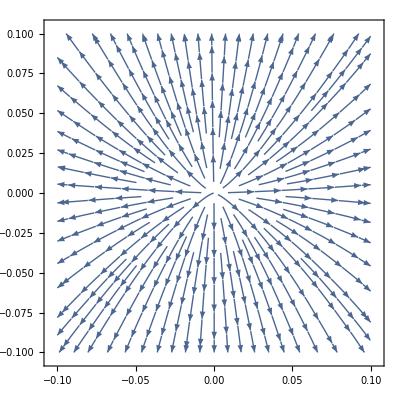

```mathematica
StreamPlot[{x*(1.5-x-0.5*y),y*(2-y-0.75*x)},{x,-.1,.1},{y,-.1,.1}]
```

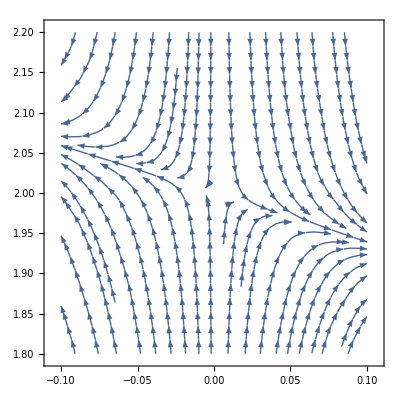

```mathematica
StreamPlot[{x*(1.5-x-0.5*y),y*(2-y-0.75*x)},{x,-.1,.1},{y,1.8,2.2}]
```

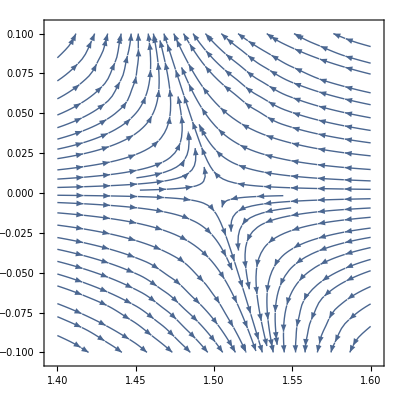

```mathematica
StreamPlot[{x*(1.5-x-0.5*y),y*(2-y-0.75*x)},{x,1.4,1.6},{y,-.1,.1}]
```

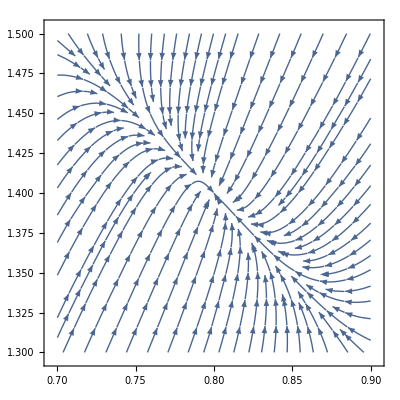

```mathematica
StreamPlot[{x*(1.5-x-0.5*y),y*(2-y-0.75*x)},{x,.7,.9},{y,1.3,1.5}]
```

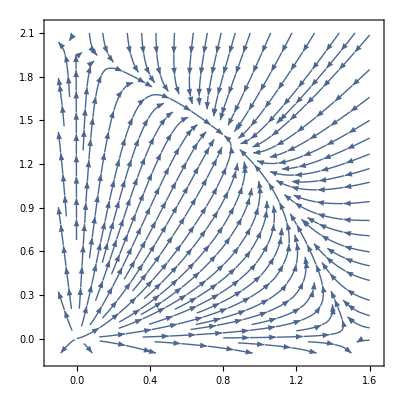

```mathematica
StreamPlot[{x*(1.5-x-0.5*y),y*(2-y-0.75*x)},{x,-.1,1.6},{y,-.1,2.1}]
```